This implements some stuff from Sawin' s wonderful paper!

```mathematica
QuantumGroupsPath = "c:\\scott\\projects\\QuantumGroups\\trunk\\package\\";
AppendTo[$Path, QuantumGroupsPath];
<<QuantumGroups`
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Found precomputed data in C:\scott\projects\QuantumGroups\trunk\data

General::obspkg: "LinearAlgebra`MatrixManipulation`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
ρ[Γ_]:=(Plus@@PositiveRoots[Γ])/2
```

```mathematica
ShortDominantRoots[G2]
```

{{1,0}}

```mathematica
LongDominantRoots[G2]
```

{{0,1}}

```mathematica
LacingNumber[Subscript[(A|D|E), _]]=1;
LacingNumber[Subscript[(B|C|F), _]]=2;
LacingNumber[Subscript[G, 2]]=3;
```

```mathematica
AlcoveRoot[Γ_,l_]:=With[{lp=If[EvenQ[l],l/2,l]},
If[Divisible[lp,LacingNumber[Γ]],
LongDominantRoots[Γ]⟦1⟧,
ShortDominantRoots[Γ]⟦1⟧]
]
```

```mathematica
AlcoveRoot[G2,26]
```

{1,0}

```mathematica
WeightInAlcoveQ[Γ_,l_Integer][λ:{___Integer}]:=(And@@(NonNegative/@λ))∧(KillingForm[Γ][AlcoveRoot[Γ,l],λ+ρ[Γ]]<If[EvenQ[l],l/2,l])
```

```mathematica
AlcoveWeights[Γ_,l_]:=AlcoveWeights[Γ,l]=Module[{ar=AlcoveRoot[Γ,l],λ=ZeroVector[Rank[Γ]],p},
Reap[
While[
Sow[λ];
λ+=UnitVector[Rank[Γ],1];
While[¬ZeroVectorQ[λ]∧¬WeightInAlcoveQ[Γ,l][λ],
(* odometer *)
p=Position[λ,x_/;x>0]⟦1,1⟧;
λ⟦p⟧=0;
If[p<Rank[Γ],++λ⟦p+1⟧];
];
¬ZeroVectorQ[λ]
]
]⟦2,1⟧
]
```

```mathematica
AlcoveWeights[G2,26]
```

{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2}}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,26])/.q->Exp[2π ⅈ 1/26]]]
```

{1.,0.564681,-0.400477,1.09654,-0.845339,-0.64155,0.564681,-0.136129}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,26])/.q->Exp[2π ⅈ 3/26]]]
```

{1.,4.14811,7.34595,6.20982,4.7128,8.05516,4.14811,2.94188}

```mathematica
Length[AlcoveWeights[G2,28]]
```

10

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 3/28]]]
```

{1.,4.49396,9.09783,10.0978,4.49396,5.60388,11.5918,10.0978,5.60388,3.49396}

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 11/28]]]
```

{1.,4.49396,9.09783,10.0978,4.49396,5.60388,11.5918,10.0978,5.60388,3.49396}

```mathematica
Min[DeleteCases[%,1.]]
```

3.49396

```mathematica
FullSimplify[Last[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,28])/.q->Exp[2π ⅈ 11/28]]]
```

2 (Cos[π/7]+Sin[π/14]+Sin[(3 π)/14])

```mathematica
FullSimplify[δ/.Solve[δ^2-1==%,δ]⟦2⟧]
```

√(1+2 (Cos[π/7]+Sin[π/14]+Sin[(3 π)/14]))

```mathematica
N[%]
```

2.1199

```mathematica
Table[Length[AlcoveWeights[G2,l]],{l,24,30}]
```

{1,40,8,12,10,56,2}

```mathematica
Table[Length[AlcoveWeights[G2,l]],{l,24,60}]
```

{1,40,8,12,10,56,2,65,14,20,16,85,4,96,21,30,24,120,6,133,30,42,33,161,9,176,40,56,44,208,12,225,52,72,56,261,16}

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
PositiveDimensionNumerators[Γ_,l_]:=Cases[Cases[Range[l]-1,k_/;CoprimeQ[l,k]],k_/;And@@(Positive/@Chop[N[(qDimension[Γ][Irrep[Γ][#]]&/@AlcoveWeights[Γ,l])/.q->Exp[2π ⅈ k/l]]])]
```

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,1,11}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 5 | 1 | 10

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,12,23}]//TableForm
```

12 | 1 | 1 | 5 | 7 | 11
13 | 8 | 5 | 8
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 2 | 2 | 7 | 8 | 13
16 | 2 | 
17 | 16 | 
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 21 | 
20 | 4 | 
21 | 6 | 2 | 8 | 10 | 11 | 13 | 19
22 | 5 | 9 | 13
23 | 33 |

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,24,40}]//TableForm
```

24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
25 | 40 | 
26 | 8 | 3 | 23
27 | 12 | 13 | 14
28 | 10 | 3 | 11 | 17 | 25
29 | 56 | 
30 | 2 | 1 | 11 | 19 | 29
31 | 65 | 
32 | 14 | 
33 | 20 | 16 | 17
34 | 16 | 
35 | 85 | 
36 | 4 | 1 | 17 | 19 | 35
37 | 96 | 
38 | 21 | 
39 | 30 | 19 | 20
40 | 24 |

```mathematica
Table[{l,Length[AlcoveWeights[G2,l]],{PositiveDimensionNumerators[G2,l]}},{l,41,50}]//TableForm
```

41 | 120 | 
42 | 6 | 1 | 5 | 17 | 25 | 37 | 41
43 | 133 | 
44 | 30 | 
45 | 42 | 22 | 23
46 | 33 | 
47 | 161 | 
48 | 9 | 1 | 5 | 19 | 23 | 25 | 29 | 43 | 47
49 | 176 | 
50 | 40 |

```mathematica
Chop[N[(qDimension[G2][Irrep[G2][#]]&/@AlcoveWeights[G2,42])/.q->Exp[2π ⅈ 1/42]]]
```

{1.,3.79129,5.79129,3.79129,3.79129,4.79129}

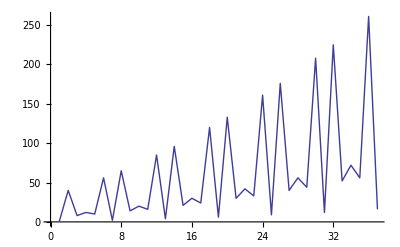

```mathematica
ListPlot[Table[Length[AlcoveWeights[G2,l]],{l,24,60}],"PlotJoined"->True]
```

```mathematica
Table[{l,Length[AlcoveWeights[A2,l]],{PositiveDimensionNumerators[A2,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 6 | 2 | 3
6 | 1 | 1 | 5
7 | 15 | 3 | 4
8 | 3 | 1 | 3 | 5 | 7
9 | 28 | 4 | 5
10 | 6 | 1 | 9
11 | 45 | 5 | 6
12 | 10 | 1 | 5 | 7 | 11
13 | 66 | 6 | 7
14 | 15 | 1 | 13
15 | 91 | 7 | 8
16 | 21 | 1 | 7 | 9 | 15
17 | 120 | 8 | 9
18 | 28 | 1 | 17
19 | 153 | 9 | 10
20 | 36 | 1 | 9 | 11 | 19

```mathematica
Chop[N[(qDimension[A2][Irrep[A2][#]]&/@AlcoveWeights[A2,7])/.q->Exp[2π ⅈ 3/7]]]
```

{1.,2.24698,2.80194,2.24698,1.,2.24698,4.04892,4.04892,2.24698,2.80194,4.04892,2.80194,2.24698,2.24698,1.}

```mathematica
%^2
```

{1.,5.04892,7.85086,5.04892,1.,5.04892,16.3937,16.3937,5.04892,7.85086,16.3937,7.85086,5.04892,5.04892,1.}

```mathematica
Table[{l,Length[AlcoveWeights[A3,l]],{PositiveDimensionNumerators[A3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 4 | 
6 | 1 | 1 | 5
7 | 20 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 56 | 
10 | 4 | 1 | 3 | 7 | 9
11 | 120 | 
12 | 10 | 1 | 11
13 | 220 | 
14 | 20 | 1 | 13
15 | 364 | 
16 | 35 | 1 | 15
17 | 560 | 
18 | 56 | 1 | 17
19 | 816 | 
20 | 84 | 1 | 19

```mathematica
Table[{l,Length[AlcoveWeights[A4,l]],{PositiveDimensionNumerators[A4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 15 | 3 | 4
8 | 1 | 1 | 3 | 5 | 7
9 | 70 | 4 | 5
10 | 1 | 1 | 3 | 7 | 9
11 | 210 | 5 | 6
12 | 5 | 1 | 5 | 7 | 11
13 | 495 | 6 | 7
14 | 15 | 1 | 13
15 | 1001 | 7 | 8
16 | 35 | 1 | 7 | 9 | 15
17 | 1820 | 8 | 9
18 | 70 | 1 | 17
19 | 3060 | 9 | 10
20 | 126 | 1 | 9 | 11 | 19

```mathematica
DualCoxeterNumber[D4]
```

6

```mathematica
Table[{l,Length[AlcoveWeights[D4,l]],{PositiveDimensionNumerators[D4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 4 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 24 | 4 | 5
10 | 1 | 1 | 3 | 7 | 9
11 | 80 | 5 | 6
12 | 1 | 1 | 5 | 7 | 11
13 | 200 | 6 | 7
14 | 4 | 1 | 3 | 5 | 9 | 11 | 13
15 | 420 | 7 | 8
16 | 11 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 784 | 8 | 9
18 | 24 | 1 | 17
19 | 1344 | 9 | 10
20 | 46 | 1 | 9 | 11 | 19

```mathematica
Chop[N[(qDimension[D4][Irrep[D4][#]]&/@AlcoveWeights[D4,7])/.q->Exp[2π ⅈ 3/7]]]
```

{1.,1.,1.,1.}

```mathematica
Chop[N[(qDimension[D4][Irrep[D4][#]]&/@AlcoveWeights[D4,9])/.q->Exp[2π ⅈ 4/9]]]
```

{1.,2.87939,2.87939,1.,4.41147,4.41147,2.87939,5.41147,2.87939,4.41147,2.87939,2.87939,1.,2.87939,5.41147,2.87939,4.41147,5.41147,5.41147,2.87939,2.87939,2.87939,2.87939,1.}

```mathematica
DualCoxeterNumber[B2]
```

3

```mathematica
Table[{l,Length[AlcoveWeights[B2,l]],{PositiveDimensionNumerators[B2,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 2 | 
6 | 1 | 1 | 5
7 | 6 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 12 | 
10 | 2 | 
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 30 | 
14 | 6 | 
15 | 42 | 
16 | 3 | 1 | 7 | 9 | 15
17 | 56 | 
18 | 12 | 
19 | 72 | 
20 | 6 | 1 | 9 | 11 | 19

```mathematica
Table[{l,Length[AlcoveWeights[B2,l]],{PositiveDimensionNumerators[B2,l]}},{l,21,40}]//TableForm
```

21 | 90 | 
22 | 20 | 
23 | 110 | 
24 | 10 | 1 | 11 | 13 | 23
25 | 132 | 
26 | 30 | 
27 | 156 | 
28 | 15 | 1 | 13 | 15 | 27
29 | 182 | 
30 | 42 | 
31 | 210 | 
32 | 21 | 1 | 15 | 17 | 31
33 | 240 | 
34 | 56 | 
35 | 272 | 
36 | 28 | 1 | 17 | 19 | 35
37 | 306 | 
38 | 72 | 
39 | 342 | 
40 | 36 | 1 | 19 | 21 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B3,l]],{PositiveDimensionNumerators[B3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 2 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 8 | 1 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 40 | 
14 | 2 | 
15 | 70 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 112 | 
18 | 8 | 
19 | 168 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Chop[N[(qDimension[B3][Irrep[B3][#]]&/@AlcoveWeights[B3,14])/.q->Exp[2π ⅈ 1/14]]]
```

{1.,-1.}

```mathematica
Chop[N[(qDimension[B3][Irrep[B3][#]]&/@AlcoveWeights[B3,18])/.q->Exp[2π ⅈ 3/18]]]
```

{1.,1.,0,-2.,0,2.,2.,-4.}

```mathematica
Table[{l,Length[AlcoveWeights[B3,l]],{PositiveDimensionNumerators[B3,l]}},{l,22,40,2}]//TableForm
```

22 | 20 | 
24 | 3 | 1 | 7 | 17 | 23
26 | 40 | 
28 | 7 | 1 | 3 | 9 | 19 | 25 | 27
30 | 70 | 
32 | 13 | 1 | 31
34 | 112 | 
36 | 22 | 1 | 35
38 | 168 | 
40 | 34 | 1 | 39

```mathematica
DualCoxeterNumber[B4]
```

7

```mathematica
Table[{l,Length[AlcoveWeights[B4,l]],{PositiveDimensionNumerators[B4,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 2 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 10 | 3 | 19
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 30 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 70 | 
32 | 3 | 1 | 7 | 9 | 15 | 17 | 23 | 25 | 31
34 | 140 | 
36 | 8 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 252 | 
40 | 16 | 1 | 19 | 21 | 39

```mathematica
Chop[N[(qDimension[B4][Irrep[B4][#]]&/@AlcoveWeights[B4,18])/.q->Exp[2π ⅈ 1/18]]]
```

{1.,1.}

```mathematica
Chop[N[(qDimension[B4][Irrep[B4][#]]&/@AlcoveWeights[B4,22])/.q->Exp[2π ⅈ 3/22]]]
```

{1.,1.91899,2.68251,3.22871,3.51334,3.22871,2.68251,1.91899,3.51334,1.}

```mathematica
Chop[N[(qDimension[B5][Irrep[B5][#]]&/@AlcoveWeights[B5,22])/.q->Exp[2π ⅈ 1/22]]]
```

{1.,1.}

```mathematica
Chop[N[(qDimension[B5][Irrep[B5][#]]&/@AlcoveWeights[B5,26])/.q->Exp[2π ⅈ 3/26]]]
```

{1.,1.94188,2.77091,3.43891,3.90704,4.14811,3.90704,3.43891,2.77091,1.94188,4.14811,1.}

```mathematica
Chop[N[(qDimension[B6][Irrep[B6][#]]&/@AlcoveWeights[B6,30])/.q->Exp[2π ⅈ 3/30]]]
```

{1.,1.61803,1.61803,1.,0,2.,-3.23607,-2.,0,2.,3.23607,-6.47214,3.23607,-4.}

```mathematica
Chop[N[(qDimension[B7][Irrep[B7][#]]&/@AlcoveWeights[B7,34])/.q->Exp[2π ⅈ 3/34]]]
```

$Aborted

```mathematica
Table[{l,Length[AlcoveWeights[B5,l]],{PositiveDimensionNumerators[B5,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 2 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 12 | 3 | 23
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 42 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 112 | 
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 252 | 
40 | 3 | 1 | 7 | 9 | 17 | 23 | 31 | 33 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B6,l]],{PositiveDimensionNumerators[B6,l]}},{l,2,40,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 2 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 14 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 56 | 
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 168 | 
40 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19 | 21 | 23 | 27 | 29 | 31 | 33 | 37 | 39

```mathematica
Table[{l,Length[AlcoveWeights[B7,l]],{PositiveDimensionNumerators[B7,l]}},{l,2,34,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 2 | 
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 16 |

```mathematica
Table[{l,Length[AlcoveWeights[B8,l]],{PositiveDimensionNumerators[B8,l]}},{l,2,36,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35

```mathematica
Table[{l,Length[AlcoveWeights[Subscript[B, 9],l]],{PositiveDimensionNumerators[Subscript[B, 9],l]}},{l,2,38,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 2 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37

```mathematica
Table[{l,Length[AlcoveWeights[Subscript[B, 10],l]],{PositiveDimensionNumerators[Subscript[B, 10],l]}},{l,2,42,2}]//TableForm
```

2 | 1 | 1
4 | 1 | 1 | 3
6 | 1 | 1 | 5
8 | 1 | 1 | 3 | 5 | 7
10 | 1 | 1 | 3 | 7 | 9
12 | 1 | 1 | 5 | 7 | 11
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
30 | 1 | 1 | 7 | 11 | 13 | 17 | 19 | 23 | 29
32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37
40 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19 | 21 | 23 | 27 | 29 | 31 | 33 | 37 | 39
42 | 2 |

```mathematica
Table[{l,Length[AlcoveWeights[C3,l]],{PositiveDimensionNumerators[C3,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 2 | 
8 | 1 | 1 | 3 | 5 | 7
9 | 8 | 
10 | 1 | 1 | 3 | 7 | 9
11 | 20 | 
12 | 1 | 1 | 5 | 7 | 11
13 | 40 | 
14 | 2 | 
15 | 70 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 112 | 
18 | 8 | 
19 | 168 | 
20 | 4 | 1 | 9 | 11 | 19

```mathematica
Table[{l,Length[AlcoveWeights[C3,l]],{PositiveDimensionNumerators[C3,l]}},{l,22,40,2}]//TableForm
```

22 | 20 | 
24 | 10 | 1 | 11 | 13 | 23
26 | 40 | 
28 | 20 | 1 | 13 | 15 | 27
30 | 70 | 
32 | 35 | 1 | 15 | 17 | 31
34 | 112 | 
36 | 56 | 1 | 17 | 19 | 35
38 | 168 | 
40 | 84 | 1 | 19 | 21 | 39

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,1,20}]//TableForm
```

1 | 1 | 0
2 | 1 | 1
3 | 1 | 1 | 2
4 | 1 | 1 | 3
5 | 1 | 1 | 2 | 3 | 4
6 | 1 | 1 | 5
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
8 | 1 | 1 | 3 | 5 | 7
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
10 | 1 | 1 | 3 | 7 | 9
11 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
12 | 1 | 1 | 5 | 7 | 11
13 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
14 | 1 | 1 | 3 | 5 | 9 | 11 | 13
15 | 4 | 
16 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15
17 | 10 | 7 | 10
18 | 1 | 1 | 5 | 7 | 11 | 13 | 17
19 | 21 | 
20 | 1 | 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19

```mathematica
Chop[N[(qDimension[F4][Irrep[F4][#]]&/@AlcoveWeights[F4,17])/.q->Exp[2π ⅈ 7/17]]]
```

{1.,4.83089,2.96595,6.53132,10.1061,5.41898,5.41898,10.6534,9.21461,8.00934}

```mathematica
%^2
```

{1.,23.3375,8.79684,42.6582,102.133,29.3653,29.3653,113.495,84.9091,64.1496}

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,21,24}]//TableForm
```

21 | 39 | 
22 | 1 | 1 | 3 | 5 | 7 | 9 | 13 | 15 | 17 | 19 | 21
23 | 66 | 
24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,25,30}]//TableForm
```

25 | 105 | 
26 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
27 | 159 | 
28 | 1 | 1 | 3 | 5 | 9 | 11 | 13 | 15 | 17 | 19 | 23 | 25 | 27
29 | 231 | 
30 | 4 |

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,32,48,2}]//TableForm
```

32 | 1 | 1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31
34 | 10 | 3 | 31
36 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23 | 25 | 29 | 31 | 35
38 | 21 | 
40 | 2 | 1 | 9 | 11 | 19 | 21 | 29 | 31 | 39
42 | 39 | 
44 | 5 | 1 | 21 | 23 | 43
46 | 66 | 
48 | 9 | 1 | 5 | 19 | 23 | 25 | 29 | 43 | 47

```mathematica
Table[{l,Length[AlcoveWeights[F4,l]],{PositiveDimensionNumerators[F4,l]}},{l,50,72,2}]//TableForm
```

$Aborted

```mathematica
DualCoxeterNumber[F4]
```

9

```mathematica
DualCoxeterNumber[E6]
```

12

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,1,23,2}]//TableForm
```

1 | 1 | 0
3 | 1 | 1 | 2
5 | 1 | 1 | 2 | 3 | 4
7 | 1 | 1 | 2 | 3 | 4 | 5 | 6
9 | 1 | 1 | 2 | 4 | 5 | 7 | 8
11 | 1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
13 | 3 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
15 | 20 | 2 | 7 | 8 | 13
17 | 78 | 8 | 9
19 | 231 | 9 | 10
21 | 573 | 10 | 11
23 | 1254 | 11 | 12

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,24,25}]//TableForm
```

24 | 1 | 1 | 5 | 7 | 11 | 13 | 17 | 19 | 23
25 | 2499 |

```mathematica
Table[{l,Length[AlcoveWeights[E6,l]],{PositiveDimensionNumerators[E6,l]}},{l,26,27}]//TableForm
```

26 | 3 | 1 | 3 | 5 | 7 | 9 | 11 | 15 | 17 | 19 | 21 | 23 | 25
27 | 4629 | 13 | 14

```mathematica
Clear[WeightInAlcoveQ2]
```

```mathematica
WeightInAlcoveQ2[Γ_,l_Integer][λ_]:=(And@@(NonNegative/@λ))∧(KillingForm[Γ][AlcoveRoot[Γ,l],λ+ρ[Γ]]<If[EvenQ[l],l/2,l])
```

```mathematica
LittelmannPathInAlcoveQ[Γ_,l_][lp_]:=And@@(WeightInAlcoveQ2[Γ,l]/@QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp])
```

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[Γ_,l_][Irrep[Γ_][λ_]⊗Irrep[Γ_][μ_]]:=
Module[{lp,compositions},
lp=LittelmannPath[Γ][{λ}];compositions=QuantumGroups`LittelmannPaths`Internals`ComposeLittelmannPaths[lp,#]&/@LittelmannPathLowerings[Irrep[Γ][μ]];
Print[Cases[compositions,(lp_/;QuantumGroups`LittelmannPaths`Internals`LittelmannPathDominantQ[lp])]];
DirectSum@@SortWeights[Γ][Cases[compositions,(lp_/;LittelmannPathInAlcoveQ[Γ,l][lp]):>Irrep[Γ][LittelmannPathEndpoint[lp]]]]
]
```

```mathematica
SteinbergFold[Γ_,i_][c_]:=c/.{Irrep[Γ][
```

```mathematica
SteinbergDecomposeRepresentation[Γ_][Irrep[Γ_][λ_]⊗Irrep[Γ_][μ_]]:=Module[{c},
Plus@@(WeightMultiplicities[Γ,Irrep[Γ][μ]]/.{κ:{___Integer},n_Integer}:>n Irrep[Γ][κ+λ])
]
```

```mathematica
SteinbergDecomposeRepresentation[G2][Irrep[G2][{1,0}]⊗Irrep[G2][{1,0}]]
```

Irrep[G_2][{-1,1}]+Irrep[G_2][{0,0}]+Irrep[G_2][{0,1}]+Irrep[G_2][{1,0}]+Irrep[G_2][{2,-1}]+Irrep[G_2][{2,0}]+Irrep[G_2][{3,-1}]

```mathematica
WeightMultiplicities[G2,Irrep[G2][{0,1}]]
```

{{{0,-1},1},{{-3,1},1},{{-1,0},1},{{1,-1},1},{{-2,1},1},{{3,-2},1},{{0,0},2},{{-3,2},1},{{2,-1},1},{{-1,1},1},{{1,0},1},{{3,-1},1},{{0,1},1}}

```mathematica
AlcoveWeights[G2,26]
```

{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2}}

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[G2,26][Irrep[G2][{0,1}]⊗Irrep[G2][{0,2}]]
```

{LittelmannPath[G_2][{{0,1},{0,2}}],LittelmannPath[G_2][{{0,1},{3,-1},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-1/2,1/3},{1,-1/3},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-3/2,1},{0,1}}],LittelmannPath[G_2][{{0,1},{3/2,-1},{-3/2,1},{3,-1}}],LittelmannPath[G_2][{{0,1},{0,-1},{0,1}}]}

DirectSum[Irrep[G_2][{0,1}],Irrep[G_2][{3,0}],Irrep[G_2][{0,2}],Irrep[G_2][{2,1}]]

```mathematica
LittelmannPathDecomposeRepresentationAtRootOfUnity[G2,26][Irrep[G2][{0,1}]⊗Irrep[G2][{1,0}]]
```

{LittelmannPath[G_2][{{0,1},{1,0}}],LittelmannPath[G_2][{{0,1},{2,-1}}],LittelmannPath[G_2][{{0,1},{1,-1}}]}

DirectSum[Irrep[G_2][{1,0}],Irrep[G_2][{2,0}],Irrep[G_2][{1,1}]]

```mathematica
LittelmannPathDecomposeRepresentation[Irrep[G2][{0,1}]⊗Irrep[G2][{1,0}]]
```

LittelmannPathDecomposeRepresentation[Irrep[G_2][{0,1}]⊗Irrep[G_2][{1,0}]]

```mathematica
lp=LittelmannPath[Subscript[G, 2]][{{0,1},{0,2}}]
```

LittelmannPath[G_2][{{0,1},{0,2}}]

```mathematica
QuantumGroups`LittelmannPaths`Internals`LittelmannPathVertices[lp]
```

{{0,0},{0,1},{0,3}}

```mathematica
WeightInAlcoveQ2[G2,26][{0,3}]
```

True

```mathematica
LittelmannPathInAlcoveQ[G2,26][lp]
```

True